# Sperm/pollen competition drives sex chromosome turnover

## Michael Scott & Matthew Osmond

This is much like van Doorn & Kirkpatrick 2007 (Nature 449:909), but with sperm/pollen competition as well. Our hypothesis is that ploidally antagonistic selection will remove the need for sexually antagonistic selection to drive sex chromosome turnover.

# First try (delete?)

## Resident life-cycle

We start with haploid selection, which occurs in sperm/pollen only. Let XAm be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an X allele at the diallelic sex-determining locus. Let YA be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an Y allele at the diallelic sex-determining locus. Let XAf be the frequency of allele A at the diallelic autosomal locus in eggs (which necessarily have an X allele at the diallelic sex-determining locus). Males make α% of their sperm/pollen Y-bearing. After selection on male gametes/pollen we then have frequencies of A (and a) in each type of gamete/pollen:

```mathematica
wbarHap=(1-α)(wA XAm+wa Xam)+α(wA YA+wa Ya);
XAms=(1-α)wA XAm/wbarHap;
Xams=(1-α)wa Xam/wbarHap;
YAs=α wA*YA/wbarHap;
Yas=α wa*Ya/wbarHap;
XAfs=XAf;
Xafs=Xaf;
```

Check that frequencies A and a in the gametes produced by each sex sum to one after selection:

```mathematica
1==XAms+Xams+YAs+Yas//Factor
1==XAfs+Xafs/.XAf->1-Xaf//Factor
```

True

True

After random mating, the frequencies of the diploid genotypes are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;
```

Check that frequencies sum to one

```mathematica
XAXA+XAXa+XaXa+XAYA+XAYa+XaYA+XaYa/.Xaf->1-XAf//Factor
```

1

Without selection, after mating the sex ratio (% male) is

```mathematica
(XAYA+XAYa+XaYA+XaYa)/(XAXA+XAXa+XaXa+XAYA+XAYa+XaYA+XaYa)/.wA->1/.wa->1/.Ya->1-YA/.Xam->1-XAm//Factor
```

α

After diploid selection (which can differ between males Mij and females Fij) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;
wbarM=MAA XAYA+MAa XAYa+MAa XaYA+Maa XaYa;
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==XAYAs+XAYas+XaYAs+XaYas//Factor
```

True

True

Finally, meiosis occurs, giving the haploid frequencies at the start of the next generation

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
XAmprime=XAYAs+(1-r)XAYas+r XaYAs;
Xamprime=XaYas+r XAYas+(1-r) XaYAs;
YAprime=XAYAs+(1-r)XaYAs+ r XAYas;
Yaprime=XaYas+r XaYAs+(1- r) XAYas;
```

Check that frequencies of haploid genotypes sum to one after meiosis

```mathematica
1==XAfprime+Xafprime//Factor
1==XAmprime+Xamprime//Factor
1==YAprime+Yaprime//Factor
```

True

True

True

## Resident equilibrium

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
};
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
XAf->XAf0+XAf1 ϵ,
XAm->XAm0+XAm1 ϵ,
YA->YA0+YA1 ϵ
};
```

Without selection, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-XAf0+XAm0),XAf0-r XAf0-XAm0+r YA0,r XAf0-r YA0}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{XAf0,XAm0}]
```

{{XAf0→YA0,XAm0→YA0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub/.sol0/.YA0->pA,{ϵ,0,1}]],ϵ,Factor]//Flatten
```

{1/2 (2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t-XAf1+XAm1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r t-pA^2 r t+XAf1-r XAf1-XAm1+r YA1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t+r XAf1-r YA1) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.XAf1->dpAXfXm+XAm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.XAf1->dpAXfXm+XAm1/.eqdpAXfXm/.XAm1->dpAXmY+YA1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.XAf1->dpAXfY+YA1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium haploid genotype frequencies are

```mathematica
eqXAf=XAf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqXAm=XAm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqYA=YA0-ϵ dpAXfY+ϵ dpAXfXm/.sol0/.YA0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The change in the equilibrium frequency of A is

```mathematica
dpA=Collect[Normal[Series[2 XAfprime+XAmprime+YAprime-(2XAf-XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.XAf->eqXAf/.XAm->eqXAm/.YA->eqYA,{ϵ,0,1}]]/4,ϵ,Simplify]//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t) ϵ}

And at equilibrium we have

```mathematica
eqpA=Solve[dpA-pA==0,pA]//FullSimplify
```

{{pA→0},{pA→1},{pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for: t>0).

Also notice that, without sperm/pollen competition, the non-trivial equilibrium does not exist when there is no sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm>0&&sAf>0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

But with sperm/pollen competition the non-trivial equilirbium can exist, even without sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]])&&(1>pA/.eqpA[[3]])&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1&&t>0,Reals]
```

sAm<0&&((sAf≤sAm&&0<hAm<1&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||(sAm<sAf<0&&((0<hAm≤(-sAf+sAm)/(2 sAm)&&0<hAf<1&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((-sAf+sAm)/(2 sAm)<hAm<(sAf+sAm)/(2 sAm)&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||((sAf+sAm)/(2 sAm)≤hAm<1&&0<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm))))

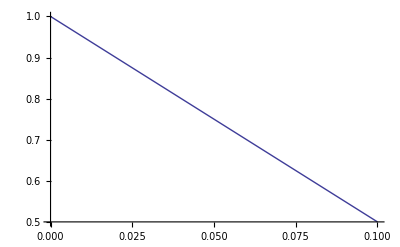

```mathematica
Plot[pA/.eqpA[[3]]/.sAf->-s/.sAm->-s/.hAf->h/.hAm->h/.s->1/10/.h->1,{t,0,1/10}]
```

### Special case

Note that when there are no sex differences in selection

```mathematica
subPAS={FAA->WAA,FAa->WAa,Faa->Waa,MAA->WAA,MAa->WAa,Maa->Waa};
```

and recombination between the autosomal and sex-determining locus is free, the equilibirum condtions become

```mathematica
differenceEqsPAS={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subPAS/.r->1/2;
```

Using the fact that the freqeuencies of A and a must sum to one in each gamete type

```mathematica
subRes={Xaf->1-XAf,Xam->1-XAm,Ya->1-YA};
```

we can directly solve for the equilibrium frequencies without assuming weak selection

```mathematica
Solve[(differenceEqsPAS/.subRes)=={0,0,0},{XAf,XAm,YA}]
```

{{XAf→0,XAm→0,YA→0},{XAf→1,XAm→1,YA→1},{XAf→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),XAm→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),YA→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA))}}

## Stability of autosomal polymorphism in the resident

Here we examine when the polymorphism on the autosomal locus (i.e., the non-trivial equilibrium frequency of A derived above) is stable. We do this not by examining the stability of the polymorphic equilibrium itself, but instead by checking when the fixation of A and a are unstable (which is mathematically easier).

We will use the fact that the frequencies of A and a in each gamete type sum to one

```mathematica
subRes={Xaf->1-XAf,Xam->1-XAm,Ya->1-YA};
```

The Jacobian is

```mathematica
matIntFull=Transpose[{D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xaf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAm],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xam],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},YA],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Ya]
}]/.subRes//Factor;
MatrixForm[%];
```

Giving characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

### When A is fixed

When A is fixed the characteristic polynomial becomes

```mathematica
charpolyInt1=charpolyIntFull/.XAf->1/.XAm->1/.YA->1;
```

With no selection the eigenvalues are

```mathematica
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→1},{λ→1/4 (1-2 r-√(9-20 r+4 r^2))},{λ→1/4 (1-2 r+√(9-20 r+4 r^2))}}

Notice that since 0<=r<=1/2 the leading eigenvalue is 1 when there is no selection.

Now assuming weak selection and looking at only the first order term, we have

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
Aλ1=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-t)}

So, combining zero and first order terms, the leading eigenvalue is 1 plus this amount, and thus the fixation of A is unstable when this amount is positive.

### When a is fixed

When a is fixed the characteristic polynomial becomes

```mathematica
charpolyInt0=charpolyIntFull/.XAf->0/.XAm->0/.YA->0;
```

With no selection the eigenvalues are

```mathematica
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→1},{λ→1/4 (1-2 r-√(9-20 r+4 r^2))},{λ→1/4 (1-2 r+√(9-20 r+4 r^2))}}

And with 0<=r<=1/2 the leading eigenvalue is 1.

With weak selection the first order term is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
aλ1=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (hAf sAf+hAm sAm+t)}

So the fixation of a is unstable when this is positive.

### Stability of polymorphism

We have a protected polymorphism on the autosomal locus in the resident population when both the fixation and loss of A is unstable, which requires that

```mathematica
Reduce[(0<δλ1/.Aλ1)&&(0<δλ1/.aλ1),Reals]
```

(sAm<0&&((sAf<0&&hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||(sAf==0&&hAm<1/2&&-hAm sAm<t<-sAm+hAm sAm)||(sAf>0&&hAf>(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)))||(sAm==0&&((sAf<0&&hAf<1/2&&-hAf sAf<t<-sAf+hAf sAf)||(sAf>0&&hAf>1/2&&-hAf sAf<t<-sAf+hAf sAf)))||(sAm>0&&((sAf<0&&hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||(sAf==0&&hAm>1/2&&-hAm sAm<t<-sAm+hAm sAm)||(sAf>0&&hAf>(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)))

## Life-cycle with rare neo-y

We now re-do the previous analyses with a rare dominant (to the X) masculinizing mutation at a new locus y. Let XAym be the frequency of A in X-bearing pollen/sperm with this new mutation, YAy be the frequency of A in Y-bearing pollen/sperm with this new mutation, and XAyf be the frequency of A in female gametes with this new mutation (this can only happen if the y mutation happened after haploids produced by diploid; otherwise the y mutation would have made the diploid male). Then, after haploid selection, the frequencies of gamete types from each sex are

```mathematica
wbarHap=(wA XAm+wa Xam+wA XAym+wa Xaym)+(wA YA+wa Ya+wA YAy+wa Yay);
XAms=wA XAm/wbarHap;
Xams=wa Xam/wbarHap;
XAyms=wA XAym/wbarHap;
Xayms=wa Xaym/wbarHap;
YAs= wA*YA/wbarHap;
Yas= wa*Ya/wbarHap;
YAys= wA*YAy/wbarHap;
Yays= wa*Yay/wbarHap;
XAfs=XAf;
Xafs=Xaf;
XAyfs=XAyf;
Xayfs=Xayf;
```

Check that frequencies of gametes types from each sex sum to one after haploid selection:

```mathematica
1==XAms+Xams+YAs+Yas+XAyms+Xayms+YAys+Yays//Factor
1==XAfs+Xafs/.Xaf->1-XAf
1==XAyfs+Xayfs/.Xayf->1-XAyf//Factor
```

True

True

True

After random mating, the frequencies of the diploid genotypes in each sex are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;
```

XX males (with a y)

```mathematica
XAyXA=XAyfs XAms+XAfs XAyms;
XAyXa=XAyfs Xams+Xafs XAyms ;
XAXay=XAfs Xayms+Xayfs XAms;
XayXa=Xayfs Xams+Xafs Xayms;
XAyXAy=XAyfs XAyms;
XAyXay=XAyfs Xayms+Xayfs XAyms ;
XayXay=Xayfs Xayms;
```

All other male types (can also carry y)

```mathematica
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;

XAyYA=XAyfs YAs;
XAyYa=XAyfs Yas;
XayYA=Xayfs YAs;
XayYa=Xayfs Yas;

XAYAy=XAfs YAys;
XAYay=XAfs Yays;
XaYAy=Xafs YAys;
XaYay=Xafs Yays;

XAyYAy=XAyfs YAys;
XAyYay=XAyfs Yays;
XayYAy=Xayfs YAys;
XayYay=Xayfs Yays;
```

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

wbarM=
MAA XAyXA+MAa(XAyXa+XAXay)+Maa XayXa+
MAA XAyXAy+MAa XAyXay+Maa XayXay+
MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa+
MAA XAyYA+MAa(XAyYa+XayYA)+Maa XayYa+
MAA XAYAy+MAa(XAYay+XaYAy)+Maa XaYay+
MAA XAyYAy+MAa(XAyYay+XayYAy)+Maa XayYay;
(*the XY males*)
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;
(*XYy males that would have been males anyway*)
XAyYAs=MAA XAyYA/wbarM;
XAyYas=MAa XAyYa/wbarM;
XayYAs=MAa XayYA/wbarM;
XayYas=Maa XayYa/wbarM;

XAYAys=MAA XAYAy/wbarM;
XAYays=MAa XAYay/wbarM;
XaYAys=MAa XaYAy/wbarM;
XaYays=Maa XaYay/wbarM;

XAyYAys=MAA XAyYAy/wbarM;
XAyYays=MAa XAyYay/wbarM;
XayYAys=MAa XayYAy/wbarM;
XayYays=Maa XayYay/wbarM;
(*the XXy males, extra males created by neoY*)
XAyXAs=MAA XAyXA/wbarM;
XAyXas=MAa XAyXa/wbarM;
XAXays=MAa XAXay/wbarM;
XayXas=Maa XayXa/wbarM;

XAyXAys=MAA XAyXAy/wbarM;
XAyXays=MAa XAyXay/wbarM;
XayXays=Maa XayXay/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==(XAyXAs+XAyXas+XAXays+XayXas+
XAyXAys+XAyXays+XayXays+
XAYAs+XAYas+XaYAs+XaYas+
XAyYAs+XAyYas+XayYAs+XayYas+
XAYAys+XAYays+XaYAys+XaYays+
XAyYAys+XAyYays+XayYAys+XayYays)//Factor
```

True

True

NOTICE THAT, the frequency of all males after diploid selection sums to 1. There are both XX (with y) and XY males. For this reason I’m not sure we can make the frequencies of X and Y pollen/sperm both sum to 1. Rather, I changed the pollen/sperm production so that the total of X and Y pollen/sperm sum to 1.

Finally, meiosis occurs, giving the haploid frequencies at the start of the next generation

Next, eggs/ovules are produced by females.

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
```

```mathematica
1==XAfprime+Xafprime//Factor
```

True

NOTE: I have put the α (fraction of Y pollen/sperm produced by a male here)

r is the recombination rate between A and Y
R is the recombination rate between y and A
χ is the recombination rate between y and Y

```mathematica
XAmprime =(1-α)(XAYAs+(XAYas(1-r)+XaYAs (r))+
(XAYAys(1-(r+R-2χ))+XAyYAs (r+R-2χ))+
(XAYays (1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)))+
(XAyXAs/2+XAyXas R/2+XAXays (1-R)/2);
Xamprime =(1-α)(XaYas+(XAYas(r)+XaYAs (1-r))+
(XaYays (1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas(r-χ)))+
(XayXas/2 +XAyXas (1-R)/2+XAXays (R)/2);
XAymprime =(1-α)(XAyYAys+(XAyYays(1-r)+XayYAys(r))+
(XAYAys(r+R-2χ)+XAyYAs(1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))))+
(XAyXAs/2+XAyXas (1-R)/2+XAXays (R)/2+XAyXAys+XAyXays/2);
Xaymprime =(1-α)(XayYays+(XAyYays(r)+XayYAys(1-r))+
(XaYays (r+R-2χ)+XayYas(1-(r+R-2χ)))+
(XAYays(r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas (χ)))+
(XayXas/2 +XAyXas (R)/2+XAXays (1-R)/2+XayXays+XAyXays/2);

YAprime =α(XAYAs+(XAYas(r)+XaYAs (1-r))+
(XAYAys(r+R-2χ)+XAyYAs (1-(r+R-2χ)))+
(XAYays (r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas(χ)));
Yaprime=α(XaYas+(XAYas(1-r)+XaYAs (r))+
(XaYays (r+R-2χ)+XayYas (1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))));
YAyprime =α(XAyYAys+(XAyYays(r)+XayYAys(1-r))+
(XAYAys(1-(r+R-2χ))+XAyYAs(r+R-2χ))+
(XAYays (χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas (r-χ)));
Yayprime =α(XayYays+(XAyYays(1-r)+XayYAys(r))+
(XaYays(1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)));
```

```mathematica
Factor[XAmprime+Xamprime+XAymprime+Xaymprime+YAprime+Yaprime+YAyprime+Yayprime]
```

1

Which might be easier to look at in this form:

First, we write use the following terms, which will then allow us to choose different gene orders and different degrees of cross-over interference. 
* RX is the chance of a double recombinant 
* RA is the chance of either one or two recombination events in a triple heterozygote
* RO is the chance of exactly one recombination event separating y and Y
* R1 is the chance of only a recombination event between y and A
* R2 is the chance of only a recombination event between A and the Y

```mathematica
subR={RA->r+Rm-χ,R0->r+Rm-2χ,R1->Rm-χ,R2->r-χ};
```

```mathematica
XAmprime =(1-α)(XAYAs+(XAYas(1-r)+XaYAs (r))+
(XAYAys(1-R0)+XAyYAs (R0))+
(XAYays (1-RA)+XayYAs(R2)+XaYAys(RX)+XAyYas(R1)))+
(XAyXAs/2+XAyXas R/2+XAXays (1-R)/2);
Xamprime =(1-α)(XaYas+(XAYas(r)+XaYAs (1-r))+
(XaYays (1-R0)+XayYas(R0))+
(XAYays(RX)+XayYAs(R1)+XaYAys(1-RA)+XAyYas(R2)))+
(XayXas/2 +XAyXas (1-R)/2+XAXays (R)/2);
XAymprime =(1-α)(XAyYAys+(XAyYays(1-r)+XayYAys(r))+
(XAYAys(R0)+XAyYAs(1-R0))+
(XAYays(R1)+XayYAs(RX)+XaYAys(R2)+XAyYas (1-RA)))+
(XAyXAs/2+XAyXas (1-R)/2+XAXays (R)/2+XAyXAys+XAyXays/2);
Xaymprime =(1-α)(XayYays+(XAyYays(r)+XayYAys(1-r))+
(XaYays (R0)+XayYas(1-R0))+
(XAYays(R2)+XayYAs(1-RA)+XaYAys(R1)+XAyYas (RX)))+
(XayXas/2 +XAyXas (R)/2+XAXays (1-R)/2+XayXays+XAyXays/2);

YAprime =α(XAYAs+(XAYas(r)+XaYAs (1-r))+
(XAYAys(R0)+XAyYAs (1-R0))+
(XAYays (R2)+XayYAs(1-RA)+XaYAys(R1)+XAyYas(RX)));
Yaprime=α(XaYas+(XAYas(1-r)+XaYAs (r))+
(XaYays (R0)+XayYas (1-R0))+
(XAYays(R1)+XayYAs(RX)+XaYAys(R2)+XAyYas (1-RA)));
YAyprime =α(XAyYAys+(XAyYays(r)+XayYAys(1-r))+
(XAYAys(1-R0)+XAyYAs(R0))+
(XAYays (RX)+XayYAs(R1)+XaYAys(1-RA)+XAyYas (R2)));
Yayprime =α(XayYays+(XAyYays(1-r)+XayYAys(r))+
(XaYays(1-R0)+XayYas(R0))+
(XAYays(1-RA)+XayYAs(R2)+XaYAys(RX)+XAyYas(R1)));
```

```mathematica
Factor[XAmprime+Xamprime+XAymprime+Xaymprime+YAprime+Yaprime+YAyprime+Yayprime/.subR]
```

(Maa wa Xam Xayf+MAa wA XAm Xayf+MAa wa Xam XAyf+MAA wA XAm XAyf+Maa wa Xaf Xaym+MAa wa XAf Xaym+Maa wa Xayf Xaym+MAa wa XAyf Xaym+MAa wA Xaf XAym+MAA wA XAf XAym+MAa wA Xayf XAym+MAA wA XAyf XAym+Maa wa Xaf Ya+MAa wa XAf Ya+Maa wa Xayf Ya+MAa wa XAyf Ya+MAa RX wa XAyf Ya+MAa wA Xaf YA+MAA wA XAf YA+MAa wA Xayf YA+MAa RX wA Xayf YA+MAA wA XAyf YA+Maa wa Xaf Yay+MAa wa XAf Yay+MAa RX wa XAf Yay+Maa wa Xayf Yay+MAa wa XAyf Yay+MAa wA Xaf YAy+MAa RX wA Xaf YAy+MAA wA XAf YAy+MAa wA Xayf YAy+MAA wA XAyf YAy-MAa wa XAyf Ya χ-MAa wA Xayf YA χ-MAa wa XAf Yay χ-MAa wA Xaf YAy χ)/(Maa wa Xam Xayf+MAa wA XAm Xayf+MAa wa Xam XAyf+MAA wA XAm XAyf+Maa wa Xaf Xaym+MAa wa XAf Xaym+Maa wa Xayf Xaym+MAa wa XAyf Xaym+MAa wA Xaf XAym+MAA wA XAf XAym+MAa wA Xayf XAym+MAA wA XAyf XAym+Maa wa Xaf Ya+MAa wa XAf Ya+Maa wa Xayf Ya+MAa wa XAyf Ya+MAa wA Xaf YA+MAA wA XAf YA+MAa wA Xayf YA+MAA wA XAyf YA+Maa wa Xaf Yay+MAa wa XAf Yay+Maa wa Xayf Yay+MAa wa XAyf Yay+MAa wA Xaf YAy+MAA wA XAf YAy+MAa wA Xayf YAy+MAA wA XAyf YAy)

## Resident equilibrium (new recursions - adjusted for the new position of α)

We will assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YA->pY*α,
Ya->(1-pY)*α,
XAyf->0,
Xayf->0,
XAym->0,
Xaym->0,
YAy->0,
Yay->0
};
```

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pY->pY0+pY1 ϵ
};
```

Without selection the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pY0 r) (1-α)+pXm0 α,pXf0 r α-pY0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pY0,pXm0→pY0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pY0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t) ϵ,(-pXf1+pXm1+pXf1 r-pY1 r-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA r t+pA^2 r t) (-1+α) ϵ,(pXf1 r-pY1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t) α ϵ}

```mathematica
Solve[differenceEqs1==0,{pXf1,pXm1,pY1}]
```

{}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.pXf1->dpAXfXm+pXm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.pXf1->dpAXfXm+pXm1/.eqdpAXfXm/.pXm1->dpAXmY+pY1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.pXf1->dpAXfY+pY1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium haploid genotype frequencies are(?)

```mathematica
eqpXf=pXf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.pY0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqpXm=pXm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.pY0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqpY=pY0+ϵ dpAXfXm-ϵ dpAXfY/.sol0/.pY0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The recursion for pA is given by

```mathematica
dpA=Collect[Normal[Series[ 2XAfprime+XAmprime/(1-α)+YAprime/α-(2XAf-XAm/(1-α)-YA/α)/.weaksel/.subequil/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY,{ϵ,0,1}]]/4,ϵ,Simplify]/.ϵ->1//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t)}

And at equilibrium we have

```mathematica
Solve[dpA-pA==0,pA]
```

{{pA→0},{pA→1},{pA→(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## Check (internal) Stability of Equilibrium (should be the same as above but need to adjust for α)

## External Stability (i.e., invasion of a neo Y)

```mathematica
subequil
```

{XAf→pXf,Xaf→1-pXf,XAm→pXm (1-α),Xam→(1-pXm) (1-α),YA→pY α,Ya→(1-pY) α,XAyf→0,Xayf→0,XAym→0,Xaym→0,YAy→0,Yay→0}

Notice that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix.

```mathematica
matExtFull=Transpose[{D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAyf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xayf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xaym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},YAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Yaym]
}]/.subequil//Factor;
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
((-1+α) (MAa wa-MAa pXm wa-MAa R wa+MAa pXm R wa+MAA pXm wA+2 MAa wa α-2 MAa pY wa α-2 MAa RA wa α+2 MAa pY RA wa α+2 MAA pY wA α-2 MAA pY R0 wA α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | (MAa wA (-1+α) (pXm R+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((MAa-MAa pXf+MAA pXf-MAa R+MAa pXf R) wA)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | -(MAa pXf R wa)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | 0 | 0
-(MAa wa (-1+α) (-R+pXm R-2 RX α+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((-1+α) (-Maa wa+Maa pXm wa-MAa pXm wA+MAa pXm R wA-2 Maa wa α+2 Maa pY wa α+2 Maa R0 wa α-2 Maa pY R0 wa α-2 MAa pY wA α+2 MAa pY RA wA α))/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | (MAa (-1+pXf) R wA)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | -((-Maa+Maa pXf-MAa pXf+MAa pXf R) wa)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | 0 | 0
((-MAa R2 wa+MAa pY R2 wa-MAA pY R0 wA) α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -(MAa pY R1 wA α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | 0 | 0 | 0 | 0
(MAa (-1+pY) R1 wa α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -((-Maa R0 wa+Maa pY R0 wa-MAa pY R2 wA) α)/(Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) | 0 | 0 | 0 | 0)

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[6]*λ];
```

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]/.χ->r*R//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1/(2 α)},{λ→(1-R)/(2 α)}}

It seems that Yy-bearing males have no effect on the invasion (would have been males anyway). The inclusion of Xiyf is also irrelevant as mutations arising in females are males in the next generation.

The first order effect is on sex ratio. If the initial population has a sex ratio bias (e.g., produces an excess of X-bearing pollen/sperm, α<1/2), then a male determiner will invade. I think an initial sex ratio bias selecting for neo sex determiners was discussed by Jim Bull ???

Here, we will assume that any deviations from α=1/2 are on the order of ϵ

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ,{ϵ,0,0}]]/.χ->r*R//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-R}}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ/.λ->1+δλ*ϵ/.frequenciessub/.sol0,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→-2 δα}}

Going to the next order in ϵ (and assuming that δα is of order ϵ^2)

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1]
```

{{δλ1→0}}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2]
```

{{δλ2→1/R(hAm pXf1 R sAm+pXf1 pY0 R sAm-2 hAm pXf1 pY0 R sAm-hAm pY1 R sAm-pY0 pY1 R sAm+2 hAm pY0 pY1 R sAm+hAm^2 pY0 sAm^2+2 hAm pY0^2 sAm^2-5 hAm^2 pY0^2 sAm^2+pY0^3 sAm^2-6 hAm pY0^3 sAm^2+8 hAm^2 pY0^3 sAm^2-pY0^4 sAm^2+4 hAm pY0^4 sAm^2-4 hAm^2 pY0^4 sAm^2+pXf1 R t-pY1 R t+2 hAm pY0 sAm t+2 pY0^2 sAm t-6 hAm pY0^2 sAm t-2 pY0^3 sAm t+4 hAm pY0^3 sAm t-hAm pY0 R sAm t-pY0^2 R sAm t+3 hAm pY0^2 R sAm t+pY0^3 R sAm t-2 hAm pY0^3 R sAm t+pY0 t^2-pY0^2 t^2-pY0 R t^2+pY0^2 R t^2-2 R δα)}}

```mathematica
frequenciessub
```

{pXf→pXf0+pXf1 ϵ,pXm→pXm0+pXm1 ϵ,pY→pY0+pY1 ϵ}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2]
```

{{δλ2→1/(r R)(2 hAf hAm pA R sAf sAm+2 hAf pA^2 R sAf sAm+2 hAm pA^2 R sAf sAm-10 hAf hAm pA^2 R sAf sAm+2 pA^3 R sAf sAm-6 hAf pA^3 R sAf sAm-6 hAm pA^3 R sAf sAm+16 hAf hAm pA^3 R sAf sAm-2 pA^4 R sAf sAm+4 hAf pA^4 R sAf sAm+4 hAm pA^4 R sAf sAm-8 hAf hAm pA^4 R sAf sAm-2 hAf hAm pA r R sAf sAm-2 hAf pA^2 r R sAf sAm-2 hAm pA^2 r R sAf sAm+10 hAf hAm pA^2 r R sAf sAm-2 pA^3 r R sAf sAm+6 hAf pA^3 r R sAf sAm+6 hAm pA^3 r R sAf sAm-16 hAf hAm pA^3 r R sAf sAm+2 pA^4 r R sAf sAm-4 hAf pA^4 r R sAf sAm-4 hAm pA^4 r R sAf sAm+8 hAf hAm pA^4 r R sAf sAm+hAm^2 pA r sAm^2+2 hAm pA^2 r sAm^2-5 hAm^2 pA^2 r sAm^2+pA^3 r sAm^2-6 hAm pA^3 r sAm^2+8 hAm^2 pA^3 r sAm^2-pA^4 r sAm^2+4 hAm pA^4 r sAm^2-4 hAm^2 pA^4 r sAm^2+2 hAf pA R sAf t+2 pA^2 R sAf t-6 hAf pA^2 R sAf t-2 pA^3 R sAf t+4 hAf pA^3 R sAf t-2 hAf pA r R sAf t-2 pA^2 r R sAf t+6 hAf pA^2 r R sAf t+2 pA^3 r R sAf t-4 hAf pA^3 r R sAf t+2 hAm pA r sAm t+2 pA^2 r sAm t-6 hAm pA^2 r sAm t-2 pA^3 r sAm t+4 hAm pA^3 r sAm t+pA r t^2-pA^2 r t^2-2 r R δα)}}

```mathematica
Collect[δλ2/.%/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm),δα,Simplify]
```

{((r-2 R+2 r R) sAf^2 (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (hAm sAm+t-hAf (sAm+2 t))^2)/(r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)-2 δα}

The denominator looks suspiciously like pA. And van Doorn and Kirkpatrick have a p(1-p) term (which is often present due to Fisher’s fundamental theorum), so I will try those substitutions.

```mathematica
((r-2 R+2 r R) sAf^2 (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (hAm sAm+t-hAf (sAm+2 t))^2)/(r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)*(pA/((hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)))//Simplify
```

-(pA (r-2 R+2 r R) sAf^2 ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAm sAm+t-hAf (sAm+2 t))^2)/(r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^3)

```mathematica
%*((1-pA)/(1-(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)))//Simplify
```

-((-1+pA) pA (r-2 R+2 r R) sAf^2 (hAm sAm+t-hAf (sAm+2 t))^2)/(r R ((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2)

I suspect the rest probably factors in the form given in van Doorn and Kirkpatrick.

They assume that the y is autosomal such that R=1/2

```mathematica
%/.R->1/2
```

-(2 (-1+pA) pA (-1+2 r) sAf^2 (hAm sAm+t-hAf (sAm+2 t))^2)/(r ((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2)

```mathematica
%*(L/((1-2r)/r))//Simplify
```

(2 L (-1+pA) pA sAf^2 (hAm sAm+t-hAf (sAm+2 t))^2)/((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2

```mathematica
%/.t->0
```

(2 L (-1+pA) pA sAf^2 (-hAf sAm+hAm sAm)^2)/((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2

I suspect these terms are really marginal fitnesses.

```mathematica
σAm=(pA+hAm(1-pA))sAm-pA hAm sAm ;
σAf=(pA+hAf(1-pA))sAf-pA hAf sAf;
σAm(σAm-σAf)/2/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)/.t->0//Simplify
```

((hAf-hAm)^2 sAf^2 sAm^2)/((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2

```mathematica
(2 L (-1+pA) pA sAf^2 (-hAf sAm+hAm sAm)^2)/((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2*SA/(((hAf-hAm)^2 sAf^2 sAm^2)/((-1+2 hAf) sAf+(-1+2 hAm) sAm)^2)//Factor
```

2 L (-1+pA) pA SA

This should be adjusted to include t, which will take some finangling.

I believe that the a locus model should essential be where we assume the r=1/2 instead of R=1/2. Thus everything is equivalent except for the labelling (R versus r and sai for sAi). 

In their other analyses I think they assume that r is of a similar order to the selection terms.

Other thoughts:
With our method we can also include an α of the new y. This is not so interesting though as non-mendelian inheritance is not thought to be that important. 
We should adjust the haploid fitnesses so that they are wXA, wXa, wYA, wYa etc. to allow general forms of selection on the haploids (e.g., if the Y has low fitness due to degeneration). 
We could also consider transitions to ZW systems by adjusting the recursion equations - I think this is where the action will be. 
With our method, we could also consider incomplete neoY systems - that is, they make males, but not all of the time (like an partial loss of female function mutation, rather than complete sterility). This would invovle the full invasion matrix, i.e., there would be Xiyf haploids to track.

# Second try (delete?)

## Life-cycle

We now re-do the previous analyses with a rare dominant (to the X) masculinizing mutation at a new locus y. We let yA be the frequency of A in pollen/sperm with this new mutation. Then, after haploid selection, the frequencies of haploid types from each sex are

```mathematica
wbarHapXm= wA XAm+ wa Xam;
wbarHapY= wA YA+ wa Ya;
wbarHapy= wA xA+ wa (1-xA);
XAms= (1-α) wA XAm/wbarHapXm;
Xams=(1-α) wa Xam/wbarHapXm;
YAs=  α wA*YA/wbarHapY;
Yas= α wa*Ya/wbarHapY;
XAfs=XAf;
Xafs=Xaf;
yAs= α wA ϵy xA/wbarHapy;
yas= α wa ϵy(1-xA)/wbarHapy;
```

Check that frequencies of gametes types from each sex sum to the appropriate fraction after haploid selection:

```mathematica
1-α==XAms+Xams/.Xam->1-XAm//Factor
α==YAs+Yas/.Ya->1-YA//Factor
1==XAfs+Xafs/.Xaf->1-XAf//Factor
α ϵy==yAs+yas//Factor
```

True

True

True

«1 more identical outputs»

After random mating, the frequencies of the diploid genotypes are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;

XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;

XAyA=XAfs yAs;
XAya=XAfs yas;
XayA=Xafs yAs;
Xaya=Xafs yas;
```

Check that frequencies sum to the appropriate fraction

```mathematica
1-α==XAXA+XAXa+XaXa/.Xaf->1-XAf/.Xam->1-XAm//Factor
α==XAYA+XAYa+XaYA+XaYa/.Ya->1-YA/.Xaf->1-XAf//Factor
α ϵy==XAyA+XAya+XayA+Xaya/.Xaf->1-XAf//Factor
```

True

True

True

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;

XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

wbarM=MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa; (*ignore rare mutants*)

XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;

XAyAs=MAA XAyA/wbarM;
XAyas=MAa XAya/wbarM;
XayAs=MAa XayA/wbarM;
Xayas=Maa Xaya/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==XAYAs+XAYas+XaYAs+XaYas//Factor
```

True

True

Finally, meiosis occurs.

Eggs/ovules are produced by females:

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
```

Check that frequencies sum to one

```mathematica
1==XAfprime+Xafprime//Factor
```

True

Pollen/sperm are produced by males:
r is the recombination rate between A and Y

```mathematica
XAmprime =XAYAs+XAYas(1-r)+XaYAs r;
Xamprime =XAYas r+XaYAs (1-r)+XaYas;

YAprime =XAYAs+XAYas r+XaYAs (1-r);
Yaprime =XAYas (1-r)+XaYAs r+XaYas;
```

Check that the frequencies of A and a sum to one in each gamete type

```mathematica
1==XAmprime+Xamprime//Factor
1==YAprime+Yaprime//Factor
```

True

True

Now, the frequency of A on the neo-y in the next generation is

```mathematica
xAprime=(XAyAs+XAyas R+XayAs (1-R))/(XAyAs+XAyas R+XayAs (1-R)+XAyas (1-R)+XayAs R+Xayas)//Factor
```

-(-MAa wA xA Xaf+MAa R wA xA Xaf-MAa R wa XAf+MAa R wa xA XAf-MAA wA xA XAf)/(Maa wa Xaf-Maa wa xA Xaf+MAa wA xA Xaf+MAa wa XAf-MAa wa xA XAf+MAA wA xA XAf)

And the growth rate of the neo-y is

```mathematica
RA=(XAyAs+XAyas R+XayAs (1-R)+XAyas (1-R)+XayAs R+Xayas)/ϵy//Factor
```

((-Maa wa Xaf+Maa wa xA Xaf-MAa wA xA Xaf-MAa wa XAf+MAa wa xA XAf-MAA wA xA XAf) (wa Ya+wA YA))/((-wa+wa xA-wA xA) (Maa wa Xaf Ya+MAa wa XAf Ya+MAa wA Xaf YA+MAA wA XAf YA))

This collapses to van Doorn and Kirkpatrick under special circumstances (bottom page 3)

```mathematica
RA/.wA->1/.wa->1/.Maa->1/.MAa->1+hAm sAm/.MAA->1+sAm/.Faa->1/.FAa->1+hAf sAf/.FAA->1+sAf/.Ya->1-YA/.Xam->1-XAm/.Xaf->1-XAf/.xa->1-xA//FullSimplify
```

(1+sAm xA XAf+hAm sAm (xA+XAf-2 xA XAf))/(1+sAm XAf YA+hAm sAm (XAf+YA-2 XAf YA))

## Equilibrium

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA,
xAprime-xA
};
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
XAf->XAf0+XAf1 ϵ,
XAm->XAm0+XAm1 ϵ,
YA->YA0+YA1 ϵ,
xA->xA0+xA1 ϵ
};
```

Without selection, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-XAf0+XAm0),XAf0-r XAf0-XAm0+r YA0,r XAf0-r YA0,-R xA0+R XAf0}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{XAf0,XAm0,YA0}]
```

{{XAf0→xA0,XAm0→xA0,YA0→xA0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub/.sol0/.xA0->pA,{ϵ,0,1}]],ϵ,FullSimplify]//Flatten
```

{1/2 ((-1+pA) pA (-2 pA sAf+2 hAf (-1+2 pA) sAf-t)-XAf1+XAm1) ϵ,(-pA^3 sAm+hAm (-1+pA) pA (-1+2 pA) sAm+pA r t+pA^2 (sAm-r t)+XAf1-r XAf1-XAm1+r YA1) ϵ,(-pA^3 sAm+hAm (-1+pA) pA (-1+2 pA) sAm+pA^2 (sAm+(-1+r) t)+pA (t-r t)+r (XAf1-YA1)) ϵ,(-pA^3 sAm+hAm (-1+pA) pA (-1+2 pA) sAm+pA^2 (sAm+(-1+R) t)+pA (t-R t)+R (-xA1+XAf1)) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.XAf1->dpAXfXm+XAm1,dpAXfXm]//Flatten
```

{dpAXfXm→(-1+pA) pA (-2 hAf sAf-2 pA sAf+4 hAf pA sAf-t)}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.XAf1->dpAXfXm+XAm1/.eqdpAXfXm/.XAm1->dpAXmY+YA1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.XAf1->dpAXfY+YA1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

The difference in the frequency of A with X in females and with y is (at equilibrium to first order in selection)

```mathematica
eqdpAyXf=Solve[differenceEqs1[[4]]==0/.xA1->dpAyXf+XAf1,dpAyXf]//Flatten
```

{dpAyXf→(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA R t+pA^2 R t)/R}

So then, to first order, the equilibrium haploid genotype frequencies are

```mathematica
eqXAf=XAf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.xA0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqXAm=XAm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.xA0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqYA=YA0-ϵ dpAXfY+ϵ dpAXfXm/.sol0/.xA0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqxA=xA0+ϵ dpAXfY-ϵ dpAXfXm+ϵ dpAyXf/.sol0/.xA0->pA/.eqdpAXfY/.eqdpAXfXm/.eqdpAyXf/.eqdpAXmY//FullSimplify
```

{(pA (r R-(-1+pA) (-2 pA r R sAf+2 hAf (-1+2 pA) r R sAf+hAm (r-R) sAm-(-1+2 hAm) pA (r-R) sAm-(r (-1+R)+R) t) ϵ))/(r R)}

```mathematica
eqxA/.t->0/.R->1/2//FullSimplify
```

{(pA (r-(-1+pA) (-2 pA r sAf+2 hAf (-1+2 pA) r sAf-(-pA+hAm (-1+2 pA)) (-1+2 r) sAm) ϵ))/r}

```mathematica
Series[RA/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm,{ϵ,0,2}]/.t->0//Simplify
```

1-sAm (-XAf+hAm (-1+2 XAf)) (xA-YA) ϵ+sAm^2 ((XAf YA+hAm (XAf+YA-2 XAf YA))^2+(xA XAf+hAm (xA+XAf-2 xA XAf)) (-XAf YA+hAm (-YA+XAf (-1+2 YA)))) ϵ^2+O[ϵ]^3

The change in the equilibrium frequency of A is

```mathematica
dpA=Collect[Normal[Series[2 XAfprime+XAmprime+YAprime-(2XAf-XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.XAf->eqXAf/.XAm->eqXAm/.YA->eqYA,{ϵ,0,1}]]/4,ϵ,Simplify]//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t) ϵ}

And at equilibrium we have

```mathematica
eqpA=Solve[dpA-pA==0,pA]//FullSimplify
```

{{pA→0},{pA→1},{pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for: t>0).

Also notice that, without sperm/pollen competition, the non-trivial equilibrium does not exist when there is no sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm>0&&sAf>0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

But with sperm/pollen competition the non-trivial equilirbium can exist, even without sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]])&&(1>pA/.eqpA[[3]])&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1&&t>0,Reals]
```

sAm<0&&((sAf≤sAm&&0<hAm<1&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||(sAm<sAf<0&&((0<hAm≤(-sAf+sAm)/(2 sAm)&&0<hAf<1&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((-sAf+sAm)/(2 sAm)<hAm<(sAf+sAm)/(2 sAm)&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||((sAf+sAm)/(2 sAm)≤hAm<1&&0<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm))))

```mathematica
Plot[pA/.eqpA[[3]]/.sAf->-s/.sAm->-s/.hAf->h/.hAm->h/.s->1/10/.h->1,{t,0,1/10}]
```

-Graphics-

Does the average selection differential disappear at equilibrium?

```mathematica
(σAm+σAf)/2/.σAm->(pA+hAm(1-2pA))ϵ sAm/.σAf->(pA+hAf(1-2pA))ϵ sAf/.eqpA[[3]]//FullSimplify
```

-(t ϵ)/2

not unless t=0

```mathematica
(σAm+σAf)/2/.σAm->(pA+hAm(1-2pA))ϵ sAm/.σAf->(pA+hAf(1-2pA))ϵ sAf/.eqpA[[3]]/.t->0//FullSimplify
```

0

or we include haploid selection in the original formulation

```mathematica
(σAm+σAf+t ϵ)/2/.σAm->(pA+hAm(1-2pA))ϵ sAm/.σAf->(pA+hAf(1-2pA))ϵ sAf/.eqpA[[3]]//FullSimplify
```

0

### Special case

Note that when there are no sex differences in selection

```mathematica
subPAS={FAA->WAA,FAa->WAa,Faa->Waa,MAA->WAA,MAa->WAa,Maa->Waa};
```

and recombination between the autosomal and sex-determining locus is free, the non-mutant (resident) equilibirum condtions become

```mathematica
differenceEqsPAS={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subPAS/.r->1/2;
```

Using the fact that the freqeuencies of A and a must sum to one in each gamete type

```mathematica
subRes={Xaf->1-XAf,Xam->1-XAm,Ya->1-YA};
```

we can directly solve for the equilibrium frequencies without assuming weak selection

```mathematica
Solve[(differenceEqsPAS/.subRes)=={0,0,0},{XAf,XAm,YA}]
```

{{XAf→0,XAm→0,YA→0},{XAf→1,XAm→1,YA→1},{XAf→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),XAm→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),YA→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA))}}

## Neo-y growth

```mathematica
pAsubs={
XAf->pA+1/3 ϵ dpAXY+ϵ dpAXfXm,
XAm->pA+1/3 ϵ dpAXY-ϵ dpAXfXm,
YA->pA-ϵ dpAXY-ϵ dpAXfXm,
xA->pA+1/3 ϵ dpAXY-ϵ dpAXfXm+2ϵ dpAxXm
};
```

```mathematica
approxRA=Series[RA/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,2}]//Simplify
```

1-2/3 ((3 dpAxXm+2 dpAXY) (-pA+hAm (-1+2 pA)) sAm) ϵ^2+O[ϵ]^3

```mathematica
eqdpAXY=Series[(2 XAfprime+XAmprime-YAprime)-(2XAf+XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

(-4 dpAXfXm r-(8 dpAXY r)/3+2 (-1+pA) pA (-pA sAf+hAf (-1+2 pA) sAf-r t)) ϵ+O[ϵ]^2

```mathematica
eqdpAXfXm=Series[(XAfprime-XAmprime)-(XAf-XAm)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

((4 dpAXY r)/3+dpAXfXm (-3+2 r)+1/2 (-1+pA) pA (2 hAf (-1+2 pA) sAf+2 hAm sAm-2 pA (sAf-sAm+2 hAm sAm)-t+2 r t)) ϵ+O[ϵ]^2

```mathematica
dpasubs1=Solve[{eqdpAXY==0,eqdpAXfXm==0},{dpAXY,dpAXfXm}]//Flatten//FullSimplify
```

{dpAXY→-1/(4 r)(-1+pA) pA (hAf (-1+2 pA) (-3+4 r) sAf+pA (3 sAf-4 r sAf+2 r sAm-4 hAm r sAm)+2 r (hAm sAm+t)),dpAXfXm→1/6 (-1+pA) pA (4 hAf (-1+2 pA) sAf+2 hAm sAm+2 pA (-2 sAf+sAm-2 hAm sAm)-t)}

```mathematica
eqdpAXmx=Series[(XAmprime-xAprime)-(XAm-xA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

(-(4 dpAXY r)/3+2 dpAxXm R-2 dpAXfXm (-1+r+R)-pA t+pA^2 t+pA r t-pA^2 r t+pA R t-pA^2 R t) ϵ+O[ϵ]^2

```mathematica
dpasubs2=Solve[{eqdpAXmx==0},{dpAxXm}]//Flatten//FullSimplify
```

{dpAxXm→(4 dpAXY r+6 dpAXfXm (-1+r+R)+3 (-1+pA) pA (-1+r+R) t)/(6 R)}

```mathematica
dpasubs3=dpasubs2/.dpasubs1//Simplify
```

{dpAxXm→1/(6 R)(-1+pA) pA (hAf (-1+2 pA) (-1+4 R) sAf+pA (sAf-4 R sAf+2 (-1+2 hAm+R-2 hAm R) sAm)+2 (-1+R) (hAm sAm+t))}

```mathematica
appRA=approxRA/.dpasubs1/.dpasubs3//FullSimplify
```

1+1/(3 r R)(-1+pA) pA (-pA+hAm (-1+2 pA)) sAm (hAf (-1+2 pA) (r-3 R) sAf+pA (3 R sAf-r (sAf-2 sAm+4 hAm sAm))+2 r (hAm sAm+t)) ϵ^2+O[ϵ]^3

```mathematica
appRA/.t->0/.R->1/2//FullSimplify
```

1+1/(3 r)(-1+pA) pA (-pA+hAm (-1+2 pA)) sAm ((-pA+hAf (-1+2 pA)) (-3+2 r) sAf+4 (hAm+pA-2 hAm pA) r sAm) ϵ^2+O[ϵ]^3

```mathematica
kirk={1-VA LA SA}/.VA->pA(1-pA)/.LA->(1-2r)/r/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-2pA))ϵ sAm/.σAf->(pA+hAf(1-2pA))ϵ sAf//FullSimplify
```

{1-1/(2 r)(1-pA) pA (hAm+pA-2 hAm pA) (1-2 r) sAm ϵ (-(hAf+pA-2 hAf pA) sAf ϵ+(hAm+pA-2 hAm pA) sAm ϵ)}

```mathematica
appRA-kirk/.eqpA[[3]]/.R->1/2/.t->0//FullSimplify
```

{O[ϵ]^3}

# 1 - Effect of a sexually-antagonistic locus on the sex chromosome

## Recursion equations

We start with haploid selection, which occurs in sperm/pollen only. Let XAm be the frequency of allele 1 at the diallelic autosomal locus A in gametes/pollen with an X allele at the original diallelic sex-determining locus (ie the frequency of A1 in male gametes with X chromosomes). Let YA be the frequency of allele 1 at the diallelic autosomal locus A in gametes/pollen with a Y allele at the diallelic sex-determining locus (ie the frequency of A1 in male gametes with Y chromosomes). Let XAf be the frequency of allele 1 at the diallelic autosomal locus A in eggs (which necessarily have an X allele at the original diallelic sex-determining locus). And let yA be the frequency of allele 1 at the diallelic autosomal locus A in pollen/sperm with a new dominant macculinizing (ie a neo-y) mutation. We assume males make α% of their sperm/pollen with Y (or y). After selection on male gametes/pollen we then have

```mathematica
wbarHapXm= wA XAm+ wa Xam;
wbarHapY= wA YA+ wa Ya;
wbarHapy= wA xA+ wa (1-xA);
XAms= (1-α) wA XAm/wbarHapXm;
Xams=(1-α) wa Xam/wbarHapXm;
YAs=  α wA*YA/wbarHapY;
Yas= α wa*Ya/wbarHapY;
XAfs=XAf;
Xafs=Xaf;
yAs= α wA ϵy xA/wbarHapy;
yas= α wa ϵy(1-xA)/wbarHapy;
```

where wA and wa describe selection in male gametes/pollen, ϵy is the (small) frequency of the neo-y mutation, and xA is the frequency of A in gametes with the neo-y.

Check that frequencies of allele 1 in each gametes type sums to the appropriate fraction after haploid selection:

```mathematica
1-α==XAms+Xams/.Xam->1-XAm//Factor
α==YAs+Yas/.Ya->1-YA//Factor
1==XAfs+Xafs/.Xaf->1-XAf//Factor
α ϵy==yAs+yas//Factor
```

True

True

True

«1 more identical outputs»

After random mating, the frequencies of the diploid genotypes are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;

XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;

XAyA=XAfs yAs;
XAya=XAfs yas;
XayA=Xafs yAs;
Xaya=Xafs yas;
```

Check that frequencies sum to the appropriate fraction

```mathematica
1-α==XAXA+XAXa+XaXa/.Xaf->1-XAf/.Xam->1-XAm//Factor
α==XAYA+XAYa+XaYA+XaYa/.Ya->1-YA/.Xaf->1-XAf//Factor
α ϵy==XAyA+XAya+XayA+Xaya/.Xaf->1-XAf//Factor
```

True

True

True

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;

XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

wbarM=MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa; (*ignore rare mutants*)

XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;

XAyAs=MAA XAyA/wbarM;
XAyas=MAa XAya/wbarM;
XayAs=MAa XayA/wbarM;
Xayas=Maa Xaya/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==XAYAs+XAYas+XaYAs+XaYas//Factor
```

True

True

Finally, meiosis occurs.

Eggs/ovules are produced by females:

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
```

Check that frequencies sum to one

```mathematica
1==XAfprime+Xafprime//Factor
```

True

Pollen/sperm are produced by males:

```mathematica
XAmprime =XAYAs+XAYas(1-r)+XaYAs r;
Xamprime =XAYas r+XaYAs (1-r)+XaYas;

YAprime =XAYAs+XAYas r+XaYAs (1-r);
Yaprime =XAYas (1-r)+XaYAs r+XaYas;
```

where r is the recombination rate between the A and original sex-determining locus.

Check that the frequencies of allele 1 sum to one in each gamete type

```mathematica
1==XAmprime+Xamprime//Factor
1==YAprime+Yaprime//Factor
```

True

True

Now, the frequency of allele 1 on the neo-y in the next generation is

```mathematica
xAprime=(XAyAs+XAyas R+XayAs (1-R))/(XAyAs+XAyas R+XayAs (1-R)+XAyas (1-R)+XayAs R+Xayas)//Factor
```

-(-MAa wA xA Xaf+MAa R wA xA Xaf-MAa R wa XAf+MAa R wa xA XAf-MAA wA xA XAf)/(Maa wa Xaf-Maa wa xA Xaf+MAa wA xA Xaf+MAa wa XAf-MAa wa xA XAf+MAA wA xA XAf)

where R is the recombination rate between the A and novel sex-determining locus.

And the growth rate of the neo-y itself is

```mathematica
RA=(XAyAs+XAyas R+XayAs (1-R)+XAyas (1-R)+XayAs R+Xayas)/ϵy//Factor
```

((-Maa wa Xaf+Maa wa xA Xaf-MAa wA xA Xaf-MAa wa XAf+MAa wa xA XAf-MAA wA xA XAf) (wa Ya+wA YA))/((-wa+wa xA-wA xA) (Maa wa Xaf Ya+MAa wa XAf Ya+MAa wA Xaf YA+MAA wA XAf YA))

This collapses to van Doorn and Kirkpatrick’s result under special circumstances (bottom page 3)

```mathematica
RA/.wA->1/.wa->1/.Maa->1/.MAa->1+hAm sAm/.MAA->1+sAm/.Faa->1/.FAa->1+hAf sAf/.FAA->1+sAf/.Ya->1-YA/.Xam->1-XAm/.Xaf->1-XAf/.xa->1-xA//FullSimplify
```

(1+sAm xA XAf+hAm sAm (xA+XAf-2 xA XAf))/(1+sAm XAf YA+hAm sAm (XAf+YA-2 XAf YA))

## Weak selection approximation

To simplify the following analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We will solve for the equilibrium frequency of allele 1 in each of the haploid genotypes. Equilibrium is achieved when the following equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA,
xAprime-xA
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
XAf->XAf0+XAf1 ϵ,
XAm->XAm0+XAm1 ϵ,
YA->YA0+YA1 ϵ,
xA->xA0+xA1 ϵ
};
```

Without selection, the recursions for the change in frequency of allele 1 in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-XAf0+XAm0),XAf0-r XAf0-XAm0+r YA0,r XAf0-r YA0,-R xA0+R XAf0}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{XAf0,XAm0,YA0}]
```

{{XAf0→xA0,XAm0→xA0,YA0→xA0}}

So, with no selection, the equilibrium frequency of allele 1 in each gamete/pollen type is equal (and we call this pA).

### Weak linkage approximation

Following van Doorn and Kirkpatrick, when recombination between the A and neo-y loci is strong relative to selection, we can write the frequencies of allele 1 in each haploid type like

```mathematica
pAsubs={
XAf->pA+1/3 ϵ dpAXY+ϵ dpAXfXm,
XAm->pA+1/3 ϵ dpAXY-ϵ dpAXfXm,
YA->pA-ϵ dpAXY-ϵ dpAXfXm,
xA->pA+1/3 ϵ dpAXY-ϵ dpAXfXm+2ϵ dpAxXm
};
```

where dpAXY is the difference in the frequency of allele 1 on X vs Y chromosomes, dpAXfXm is the difference in the frequency of allele 1 on female vs male X chromosomes, and dpAxXm is the difference in the frequency of allele 1 on X chromosomes in males with novel vs original sex determination factors.

We can then approximate the growth rate of the neo-y as

```mathematica
approxRA=Series[RA/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,2}]//Simplify
```

1-2/3 ((3 dpAxXm+2 dpAXY) (-pA+hAm (-1+2 pA)) sAm) ϵ^2+O[ϵ]^3

The recursion for dpAXY is

```mathematica
eqdpAXY=Series[(2 XAfprime+XAmprime-YAprime)-(2XAf+XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

(-4 dpAXfXm r-(8 dpAXY r)/3+2 (-1+pA) pA (-pA sAf+hAf (-1+2 pA) sAf-r t)) ϵ+O[ϵ]^2

The recursion for dpXfXm is

```mathematica
eqdpAXfXm=Series[(XAfprime-XAmprime)-(XAf-XAm)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

((4 dpAXY r)/3+dpAXfXm (-3+2 r)+1/2 (-1+pA) pA (2 hAf (-1+2 pA) sAf+2 hAm sAm-2 pA (sAf-sAm+2 hAm sAm)-t+2 r t)) ϵ+O[ϵ]^2

And at equilibrium we have

```mathematica
dpasubs1=Solve[{eqdpAXY==0,eqdpAXfXm==0},{dpAXY,dpAXfXm}]//Flatten//FullSimplify
```

{dpAXY→-1/(4 r)(-1+pA) pA (hAf (-1+2 pA) (-3+4 r) sAf+pA (3 sAf-4 r sAf+2 r sAm-4 hAm r sAm)+2 r (hAm sAm+t)),dpAXfXm→1/6 (-1+pA) pA (4 hAf (-1+2 pA) sAf+2 hAm sAm+2 pA (-2 sAf+sAm-2 hAm sAm)-t)}

The recursion for dpAxXm is

```mathematica
eqdpAxXm=Series[(xAprime-XAmprime)-(xA-XAm)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]//Simplify
```

((4 dpAXY r)/3-2 dpAxXm R+2 dpAXfXm (-1+r+R)+pA t-pA^2 t-pA r t+pA^2 r t-pA R t+pA^2 R t) ϵ+O[ϵ]^2

And at equilibrium

```mathematica
dpasubs2=Solve[{eqdpAxXm==0},{dpAxXm}]//Flatten//FullSimplify
```

{dpAxXm→(4 dpAXY r+6 dpAXfXm (-1+r+R)+3 (-1+pA) pA (-1+r+R) t)/(6 R)}

Subbing in the previous equilibrium result gives

```mathematica
dpasubs3=dpasubs2/.dpasubs1//Simplify
```

{dpAxXm→1/(6 R)(-1+pA) pA (hAf (-1+2 pA) (-1+4 R) sAf+pA (sAf-4 R sAf+2 (-1+2 hAm+R-2 hAm R) sAm)+2 (-1+R) (hAm sAm+t))}

Thus, at equilibrium, the growth rate of the rare neo-y is

```mathematica
appRA=approxRA/.dpasubs1/.dpasubs3//FullSimplify
```

1+((-1+pA) pA (-pA+hAm (-1+2 pA)) sAm (hAf (-1+2 pA) (r-3 R) sAf+pA (3 R sAf-r (sAf-2 sAm+4 hAm sAm))+2 r (hAm sAm+t)) ϵ^2)/(3 r R)+O[ϵ]^3

Finally, when the neo-y is rare, the change in the frequency of allele 1 is

```mathematica
dpA=Series[2 XAfprime+XAmprime+YAprime-(2XAf+XAm+YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubs,{ϵ,0,1}]/4//Flatten
```

1/2 (hAf pA sAf+pA^2 sAf-3 hAf pA^2 sAf-pA^3 sAf+2 hAf pA^3 sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t) ϵ+O[ϵ]^2

And at equilibrium we have

```mathematica
eqpA=Solve[dpA==0,pA]//FullSimplify
```

{{pA→0},{pA→1},{pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

We can now use this in the expression for the neo-y growth rate. To check our work, the growth rate should reduce to Kirkpatrick’s result when there is no haploid selection and there is free recombination between the A locus and the novel sex determination locus

```mathematica
kirk={1-VA LA SA}/.VA->pA(1-pA)/.LA->(1-2r)/r/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-2pA))ϵ sAm/.σAf->(pA+hAf(1-2pA))ϵ sAf;
appRA-kirk/.eqpA[[3]]/.t->0/.R->1/2//FullSimplify
```

{O[ϵ]^3}

### Tight linkage approximation

When recombination between the original sex-determining locus and the A locus is of the same order (or greater) as selection on the A locus, we can no longer assume the difference in the frequency of allele 1 with the X and Y to be small. Following van Doorn and Kirkpatrick, we use the new change of variables

```mathematica
pAsubsLinked={
XAf->pAX+ϵ dpAXfXm,
XAm->pAX-2ϵ dpAXfXm,
YA->pAY,
xA->pAX+ϵ dpAxX,
r->ϵ r1
};
```

where pAX and pAY are the average frequencies of allele 1 on X and Y chromosomes and dpAxX is the difference in the frequency of allele 1 with the novel sex-determining factor vs the original sex-determining factor.

An approximation for the growth rate of the neo-y is then

```mathematica
approxRALinked=Series[RA/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubsLinked,{ϵ,0,1}]//Simplify
```

1-(-pAX+hAm (-1+2 pAX)) (pAX-pAY) sAm ϵ+O[ϵ]^2

The difference in the frequency of allele 1 on the X and Y chromosomes is then approximately

```mathematica
eqpAXYLinked=Series[(2XAfprime+XAmprime-3YAprime)-(2XAf+XAm-3YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubsLinked,{ϵ,0,1}]//FullSimplify
```

(2 (-1+2 hAf) pAX^3 sAf-pAX^2 ((-2+6 hAf) sAf+(hAm+pAY-2 hAm pAY) sAm+t)+pAX (-4 r1+2 hAf sAf+pAY (-2+3 pAY) sAm+hAm (1+4 pAY-6 pAY^2) sAm+t)+pAY (4 r1+3 (-1+pAY) (hAm sAm+t))) ϵ+O[ϵ]^2

And the rate of change in the average frequency of allele 1 is

```mathematica
eqpALinked=Series[(2XAfprime+XAmprime+YAprime)-(2XAf+XAm+YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.pAsubsLinked,{ϵ,0,1}]//FullSimplify
```

(-2 pAX^3 sAf+2 hAf (-1+pAX) pAX (-1+2 pAX) sAf+pAX^2 (2 sAf-pAY sAm+hAm (-1+2 pAY) sAm-t)-(-1+pAY) pAY (hAm sAm+t)+pAX (-(-2+pAY) pAY sAm+hAm (1+2 (-2+pAY) pAY) sAm+t)) ϵ+O[ϵ]^2

We can simplify these expressions with some new terms

```mathematica
simplesubs={
σAX->2/3(pAX+hAf(1-2pAX))ϵ sAf+1/3(pAY+hAm(1-2pAY))ϵ sAm,
σAY->(pAX+hAm(1-2pAX))ϵ sAm,
VAX->(1-pAX)pAX,
VAY->(1-pAY)pAY
};
```

We can then write the recursion for the difference in the frequency of allele 1 with X and Y like

```mathematica
eqpAXYLinkedSimp=-4(pAX-pAY)r+3(VAX σAX-VAY σAY)+(VAX-3VAY)t ϵ;
```

Check that this is indeed true

```mathematica
eqpAXYLinkedSimp-eqpAXYLinked/.simplesubs/.r->r1 ϵ//Simplify
```

O[ϵ]^2

And therefore at equilibrium we have

```mathematica
Solve[0==eqpAXYLinkedSimp/.pAX-pAY->dpAXY,dpAXY]
```

{{dpAXY→(t VAX ϵ-3 t VAY ϵ+3 VAX σAX-3 VAY σAY)/(4 r)}}

Similarly, we can write the change in the frequency of allele 1 as

```mathematica
eqpALinkedSimp=3VAX σAX+VAY σAY+(VAX+VAY)t ϵ;
```

And check that this is indeed correct

```mathematica
eqpALinkedSimp-eqpALinked/.simplesubs/.r->r1 ϵ//Simplify
```

O[ϵ]^2

Therefore at equilibrium we have

```mathematica
variances=Solve[{eqpALinkedSimp==0,VA==(3VAX+VAY)/4},{VAX,VAY}]//Simplify//Flatten
```

{VAX→(4 VA (t ϵ+σAY))/(2 t ϵ-3 σAX+3 σAY),VAY→-(4 VA (t ϵ+3 σAX))/(2 t ϵ-3 σAX+3 σAY)}

where VA is the average variance in the frequency of allele 1 across all chromosomes.

Finally, we can write the growth rate of the neo-y like

```mathematica
RAsimp=1-σAY (3(-VAX σAX+VAY σAY))/(4 r);
```

This reduces to van Doorn and Kirkpatrick’s result in the absence of haploid selection

```mathematica
RAsimp/.variances/.t->0//FullSimplify
```

1-(4 VA σAX σAY^2)/(r σAX-r σAY)

And we check that this new expression is actually true

```mathematica
approxRALinked-RAsimp/.simplesubs//Simplify
```

(hAm+pAX-2 hAm pAX) (pAX-pAY) sAm ϵ+O[ϵ]^2

It doesn’t seem to be (why?!). But we could instead write the neo-y growth rate like

```mathematica
RAsimp2=1-σAY(pAY-pAX);
```

And this seems to be correct

```mathematica
approxRALinked-RAsimp2/.simplesubs//Simplify
```

O[ϵ]^2